# Attributing Precipitation to Circulation Using Convolutional Neural Network

## From Hourly to Monthly Scale

Baoxiang Pan
2017.7.13

## Abstract

Version 1

Precipitation prediction in dynamical weather and climate models depends on 1) the predictability of pressure or geopotential height for the forecasting period and 2) the successive work of interpreting the pressure field in terms of precipitation events. The later task is parameterized in numerical models, where iterative discretized computing inevitably blurs the hidden cause-and-effect relationship in precipitation generation. Given the continuity constraints and computing cost, it is difficult to devise what-if experiments regarding the specific impacts of  location, coverage, intensity and spatial structure of dominating circulation patterns.  While classical synoptical analysis approaches are very often limited for causation analysis of spatially distributed high dimensional data, a Convolutional Neural Network is developed here to relate precipitation field to circulation. Case study carried over West Coast United States during boreal winter showed that the network can locate and capture key pressure zones of different structures to project precipitation distribution with high accuracy across hourly to monthly scales. This direct connection between atmospheric circulation and precipitation offers a probe for attributing precipitation to the coverage, location, intensity and spatial structure of characteristic pressure zones, which can be used for model diagnosis and improvement.

Version 2

Precipitation prediction in dynamical weather and climate models depends on 1) the predictability of pressure for the forecasting period and 2) the successive work of interpreting the pressure field in terms of precipitation events. The later task is parameterized in numerical models, where iterative discretized computing inevitably blurs the hidden cause-and-effect relationship in precipitation generation. xxx about causality analysis. Given this, a Convolutional Neural Network is developed here to relate precipitation field to circulation. Case study carried over West Coast United States during boreal winter showed that the network can locate and capture key pressure zones of different structures to project precipitation distribution with high accuracy across hourly to monthly scales. This direct connection between atmospheric circulation and precipitation offers a probe for attributing precipitation to the coverage, location, intensity and spatial structure of characteristic pressure zones, which can be used for model diagnosis and improvement.

## Introduction

Version 1

Precipitation is accompanied by low pressure systems. Such connection has long been used for rainfall warning as conveyed in old proverbs. Rather than seeking immediate upcoming depression evidences in nature, the very first attempt for Quantitative Precipitation Forecast(QPF)  relies on extending pressure forecast period by interpolating barometric observations in space and extrapolating them along time, followed by the successive work of interpreting the pressure field in terms of precipitation events\cite[]. Since then, pressure prediction has been transforming from empirical inferences to accurate science due to the elucidation of physical laws, increasing computing power and densifying observation networks\cite[]. Such progress poses both opportunity and challenge on the subsidiary work of connecting precipitation to circulation.

Precipitation processes are parameterized to close the governing equation set that describes the evolution of weather. Pragmatic simulation involves equations’ discretizing and iterative computing, which would inevitably blur the hidden cause-and-effect relationship in precipitation generation. As a result, it is difficult to attribute QPF errors to specific aspects of circulation deviations. For instance, significant QPF errors may arise from poor estimation of low pressure location, depression intensity, spatial coverage or their combinations.  However, no existed approaches were found to separate and quantify the contribution of each aspect. To fill this gap helps revealing the dynamical origin of QPF deviations and sharpening our understanding of  precipitation patterns in the context of changing climate. 

Given the continuity constraint and computing cost, it’s difficult to devise what-if experiments regarding the specific impacts of circulation structures. Statistical synoptic analysis acts as important supplement for such causality identification work. For instance, correlation field map, which contours the correlation coefficients between target variable and variable on each field grid point, is both simple and effective in correlating point variable to 2-D field. For field to field mapping, Combined Principal Component Analysis(CPCA) is frequently applied. It extracts the dominant variability of the combined two or more spatial variables. This is achieved through re-projecting the combined field to the orthogonal basis set that is constructed with the eigen vectors of the original field’s covariance matrix. Other methods include  Canonical Correlation Analysis (CCA) , Singular Value Decomposition(SVD), etc.. 

Despite their effectiveness for linear space, these classical approaches are very often limited for causality analysis in high dimensional nonlinear correlated data. For example, correlation field analysis shows that at monthly scale, regional average precipitation across United States is correlated with corresponding critical point’s Sea Level Pressure(SLP) \cite[1,2,3]. This relation emerges from the frequent pass of cyclone trajectories within relatively confined regions. However, it becomes invalid at finer spatial temporal scales, where individual precipitation event actually happens\cite[].  There remains the question of how precipitation distribution is attributed to different aspects of circulation.  The “big data” provided by numerical simulation, reanalysis and observation networks calls for finer causality analysis for people to digest and realize their use.

The past decades have seen a revolution in statistics community as it keeps absorbing machine learning techniques to meet the big data challenge. Machine learning is a sub discipline in computer science focusing on solving tasks that are easy for people to perform but hard to describe formally\cite[ian goodfellow]. Here the task refers to quantifying the connection between pressure and precipitation field at finer spatial and temporal scales than our previous empirical understandings and crude causality analysis. 

Machine learning differs from strictly static computing programs in that it can learn from and make predictions on data by tuning its parameters once the algorithm paradigm is determined.  Most machine learning paradigms have found their applications in geoscience, such as tree-type models\cite[], kernel models\cite[], graphic models\cite[] and ensemble models\cite[]. The community in turn learns to treat geo variables and their connections as information and information flows to measure our knowledge of data and model\cite[myself]. 

Deep learning is branch of machine learning that attracts recent popularity for its outstanding fitting capacity. Mathematically it is a hierarchical superposition of basic non-linear units(named Neurons for their biological inspiration) that map input tensors to output tensors. The multi-layer feedforward structure allows attributing the mapping error to each computing unit by applying calculus Chain Rule to the stacked layers. Parameters(connecting weights and biases) can thus be adjusted accordingly. The flexibility
 different types of layers have evolved for
various purposes. One type of layer that warrants particular mention is convolutional
layers [48].

Among various deep learning architectures, Convolutional Neural Network(CNN) is especially suited for processing spatial structured data. The initial layers in CNN are used for seeking and optimizing inputs’ features, which are fed to the rest layers for classification/regression tasks.

Version 2

Precipitation is accompanied by low pressure systems. This connection has long been used for rainfall warning as conveyed in old proverbs. Not limited to seeking immediate upcoming depression evidences in nature, the very first attempt for Quantitative Precipitation Forecast(QPF)  relies on extending pressure forecast period by interpolating barometric observations in space and extrapolating them along time, followed by the successive work of interpreting the pressure field in terms of precipitation events\cite[]. Since then, pressure prediction has been transforming from empirical inferences to accurate science due to the elucidation of physical laws, increasing computing power and densifying observation networks\cite[]. Such progress poses both opportunities and challenges on the subsidiary work of connecting precipitation to circulation.

Precipitation processes are parameterized to close the governing equation set that describes the evolution of weather. Pragmatic simulation involves equations’ discretizing and iterative computing, which would inevitably blur the hidden cause-and-effect relationship in precipitation generation. It is difficult to attribute QPF errors to specific aspects of circulation deviations, since no easy what-if experiments regarding the specific impacts of circulation structures could be devised, given its continuity constraint and computing cost. Significant QPF errors may arise from poor estimation of low pressure location, depression intensity, spatial coverage or their combinations. However, no existed approaches were found to separate and quantify the contribution of each aspect. To fill this gap helps revealing the dynamical origin of QPF deviations and sharpening our understanding of  precipitation patterns in the context of changing climate. 

Statistical synoptic analysis plays important role in such causality identification work. For instance, correlation field map, which contours the correlation coefficients between target variable and variable on each field grid point, is both simple and effective in connecting point variable to 2-D field. For field to field mapping, Combined Principal Component Analysis(CPCA) is frequently adopted. In CPCA, dominant variability of the combined two or more spatial variables are extracted  through projecting the combined field to the orthogonal basis set, which is constructed with the eigen vectors of the original field’s covariance matrix. Other methods include Canonical Correlation Analysis (CCA) , Singular Value Decomposition(SVD), etc.. 

Despite their effectiveness for linear space, these classical approaches are very often limited for causality analysis in high dimensional nonlinearly correlated data. For example, correlation field analysis shows that at monthly scale, regional average precipitation across United States is correlated with fixed critical point’s pressure\cite[1,2,3]. This relation emerges from the frequent pass of cyclone trajectories within relatively confined regions. However, it becomes invalid at finer spatial temporal scales, where individual precipitation event actually happens\cite[].  There remains the question of how precipitation distribution is attributed to different aspects of circulation. The “big data” provided by numerical simulation, reanalysis and observation networks calls for finer causality analysis for people to digest and realize their use.

The past decades have seen a revolution in statistics community as it keeps absorbing machine learning techniques to meet the big data challenge. Machine learning is a sub discipline in computer science focusing on solving tasks that are easy for people to perform but hard to describe formally\cite[ian goodfellow]. Here the task refers to quantifying the connection between pressure and precipitation field at finer spatial and temporal scales than crude causality analysis, but more holistic than detailed numerical simulations. 

Machine learning differs from strictly static computing programs in that it can learn from and make predictions on data by tuning its parameters once the algorithm paradigm is determined.  Most machine learning paradigms have found their applications in geoscience, such as tree-type models\cite[], kernel models\cite[], graphic models\cite[] , reinforcement learning models and ensemble models\cite[]. The community in turn learns to treat geo variables and their connections as information and information flows to measure our knowledge of data and model\cite[myself]. 

Among various machine learning paradigms, deep learning is a fast-growing branch featured by its outstanding fitting capacity. Mathematically it is a hierarchical superposition of basic non-linear units(named “neurons” for their biological inspiration) that map input tensors to output tensors. The multi-layer feedforward structure allows attributing the mapping error backward to each computing unit by applying calculus Chain Rule. Parameters(connecting weights and biases) can thus be adjusted accordingly. Different layers have been developed and stacked in certain manners for various purposes. Among them, Convolutional Neural Network(CNN) attracts particular attention of the geo community for its superiority in processing spatial structured data.  Existed geological applications of CNN include short range weather prediction[24], precipitation nowcasting[25], extreme weather detection[26, 27], etc.. We illustrate how CNN can be applied for bridging the gap between coarse causality analysis and complicated numerical simulation in attributing precipitation to circulation here. 

The rest of the paper is organized as follows, we first introduce the study area and data. In the following section the details for extracting dominant pressure structures for precipitation projection using CNN are explained. Several experiments regarding different temporal scales and data sources were devised. The network is constructed and verified with reanalysis and ensemble numerical simulation data. We conclude by responding to the research questions mentioned above.

## Data and Materials

Study Areas

The West Coast United States, including California, Oregon and Washington State, was selected as case study area. We focus on its rainy season from October to March. This is based on the following reasons:
1, There is strong hydrometeorological connectivity within the research area during boreal winter time. In the West Coast United States, spatial distribution of winter precipitation largely follows the meridional progression of jet streams. Accelerating jets suck up air from the polar front, where warm moist tropical air mix with cold polar air to form convective motion accompanied by intensive precipitation and poleward transporting energy. Given limited potential energy to trigger jet streams, precipitation amount in southern and northern part are significantly negatively correlated, based on the data used in this study. This confirmed the necessity to treat the area as a whole regarding its water resources.
2, Precipitation extremes are frequently threatening the research area due to the elusiveness of  storm tracks. For instance, while the deficit of winter precipitation from 2011 to 2015 brought significant agriculture crisis and ecosystem problems[1, 2], the following winter season of 2016 to 2017 has witnessed successive storms that triggered potential infrastructure failures such as Oroville Dam and Pfeiffer Canyon Bridge. Better understanding and Early warning of these extremes are of great importance for water resources management and disaster preparation.
3, Recorded annual precipitation can range from 20 inches to over 150 inches within a distance of 60 miles under topographic influences in this area\cite[Relations between Topography and Annual Precipitation in Western Oregon and Washington]. This sets a perfect battlefield for highlighting the CNN model’s capacity in projecting precipitation spatial distribution to circulation.
4, The moisture source of precipitation in this area is abundant as it comes from eastern Pacific. This simplifies the task by limiting the precipitation dominators to dynamics apart from moisture constrains.

Data

Both gauge based and reanalysis circulation and precipitation data were used in this work. Circulation was represented by Sea Level Pressure(SLP) and Geo Potential Height(GPH)  from two widely used reanalysis datasets: the National Centers for Environmental Prediction(NCEP) and National Center for Atmospheric Research(NCAR)[28](data available at https://www.esrl.noaa.gov/psd/data/gridded/data.ncep.reanalysis.surface.html), and the

The precipitation dataset was provided by National Oceanic and Atmo- spheric Administration(NOAA) Climate Prediction Center(CPC) through averaging the gauge based daily precipitation data at monthly scale[29](data available at https://www.esrl.noaa.gov/psd/data/gridded/data.unified.daily.conus.html). The dataset covers the whole Contiguous United States(CONUS) with spatial resolution of 0.25◦ × 0.25◦. A subset covering California, Oregon and Washing-
ton State was cut out for use in this research.

The pressure field was represented by reanalysis Sea Level Pressure(SLP) data provided by the National Centers for Environmental Prediction(NCEP) and National Center for Atmospheric Research(NCAR)[28](data available at https://www.esrl.noaa.gov/psd/data/gridded/data.ncep.reanalysis.surface.html). While Geo Potential Height(GPH) data provide similar skill for precipitation projection[19], SLP data were chosen here following previous work[16]. Spatial resolution of the dataset is 2.5◦ × 2.5◦ covering whole globe. We took a rectangle subset of it covering 20◦N to 65◦N, 100◦W to 160◦W, which is large enough to capture the synoptic phenomena for the research area. We also took the reanalysis monthly precipitation data for comparison purpose.
The precipitation dataset was provided by National Oceanic and Atmo- spheric Administration(NOAA) Climate Prediction Center(CPC) through averaging the gauge based daily precipitation data at monthly scale[29](data available at https://www.esrl.noaa.gov/psd/data/gridded/data.unified.daily.conus.html). The dataset covers the whole Contiguous United States(CONUS) with spatial resolution of 0.25◦ × 0.25◦. A subset covering California, Oregon and Washing-
ton State was cut out for use in this research.

XX experiment scenarios regarding different time and spatial scales, data sources were devised. 

6 hour 
1 day
7 days
15 days
monthly

NCEP/ECMWF->NCEP/ECMWF
NCEP/ECMWF->Gauge

Precipitation (all measured in mm/hr)

#### NCEP_Reanalysis

```mathematica
NCEPprecip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]];
	mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]];	
	Table[Import["prate.sfc.gauss."<>ToString[year]<>".nc",{"Datasets","prate"}][[;;,21;;31,126;;133]]*3600,
		{year,1948,2017}]];
Block[{mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]],
	   mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]]},
	{MinMax[mlat],MinMax[mlon]}]
```

{{31.4281,50.4752},{234.375,247.5}}

```mathematica
PDFPlot[Flatten[NCEPprecip[[;;,;;,3,8]]]]
PDFPlot[Flatten[NCEPprecip[[;;,;;,3,1]]]]
```

PDFPlot[{0.,0.,0.,0.,0.,0.00719922,0.00359919,0.,0.0143993,0.115199,0.0611996,0.,0.00359919,0.,0.00359919,0.0467995,0.,0.,0.,0.,0.0107992,0.00719922,101468,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}]
 |  |  |  |

PDFPlot[{0.143999,0.345599,0.0539996,0.2016,0.5364,0.331199,0.136799,0.6012,0.0287994,0.,0.356399,0.460799,0.374399,0.1836,101484,0.,0.0216,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}]
 |  |  |  |

#### ECMWF_Reanalysis

#### CPC_Gauge

```mathematica
CPCprecip=Block[{mlat,mlon,tt,precip1,precip2},
	SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
	mlat=Import["precip.V1.0.1948.nc",{"Datasets","lat"}][[48;;]];
	mlon=Import["precip.V1.0.1948.nc",{"Datasets","lon"}][[21;;65]];
	tt=Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	       t},
			t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
			Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t]];
	precip1=Table[Block[{precip},
		precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip],{year,1948,2006}];
	precip1
	(*precip2=Block[{precip},
		precip=Import["precip.V1.0.2007_2017.nc",{"Datasets","rain"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip];
	{precip1,precip2}*)];
```

```mathematica
Dimensions[CPCprecip[[1]]]
Dimensions[CPCprecip]
```

{366,73,45}

{59}

Sea Level Pressure

#### NCEP_Reanalysis

```mathematica
NCEPslp=Block[{mlat,mlon,slat=10,elat=30,slon=85,elon=105},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/SLP"];
	mlat=Import["slp.1948.nc",{"Datasets","lat"}][[slat;;elat]];
	mlon=Import["slp.1948.nc",{"Datasets","lon"}][[slon;;elon]];
	Table[Import["slp."<>ToString[year]<>".nc",{"Datasets","slp"}][[;;,slat;;elat,slon;;elon]],
		{year,1948,2017}]];
```

```mathematica
Dimensions[precip[[1]]]
Dimensions[NCEPslp]
```

Part::partd: Part specification precip⟦1⟧ is longer than depth of object.

{2}

{70}

#### ECMWF_Reanalysis

## Methodology

Convolutional Neural Network

This part explains the idea behind Convolutional Neural Network through illustrating it with the precipitation circulation connection problem. 
Basic deep learning algorithms, such as fully connected Artificial Neural Network(ANN), have long been applied for classification/regression problems in the geo community[38, 39, 40]. While the spatial structures of inputs are very often ignored in these lumped models, they could be utilized for more compact and effective information abstraction, thereafter leading to better classification/regression results. In CNN, this is achieved  through sequentially applying two peculiar matrix operators, namely convolutional layer and pooling layer.
Each convolutional layer operator filters the input field with a same kernel, which is a m×n matrix consisted
of weight parameters. m and n are called kernel size.

The pooling layer acts as a sub-sampling layer, which can also be viewed as a convolutional layer with a maximum value selection kernel.

CNN differs from existed pattern recognition algorithms in that, instead of seeking prefixed/engineered features(or in other words, prefixed/engineered kernels), kernels of the convolutional layers could be optimized through backpropagation[20], just as any other parameters in the fully connected ANN. Thus, both the feature selection and following classification/regression process are trainable. Through optimized convolution and pooling operations, CNN maintains and extracts input’s structures toward better representation for a given target. Besides, the sharing parameter scheme can effectively reduce overfitting by lowering model complexity. We also included state-of-the-art regularization methods, such as dropout[42] and batch normalization[43], to further balance training and test performances.

Specific to the research question here, the SLP field data was fed to a CNN. Through sequentially convolution and pooling operations, we reached a new representation of the original field data, where important pressure structure information at different locations is strengthened. It was flattened and further processed through a fully connected ANN to regress precipitation distribution, where the location information is stressed by attributing different weights to neurons from different positions. Figure 6 illustrated how CNN worked on SLP using meteorological records of December,2015 as an example.
The specific CNN architecture and hyperparameters were listed in Table 2. Hyperparameters were chose through trial and error.

Benchmark models

Experiments Design

## Results

## 6 hour

NCEP->NCEP

ECMWF->ECMWF

## 1 day

NCEP->NCEP

NCEP->Gauge

ECMWF->ECMWF

ECMWF->Gauge

## 3 day

NCEP->NCEP

NCEP->Gauge

ECMWF->ECMWF

ECMWF->Gauge

## 7 days

NCEP->NCEP

NCEP->Gauge

ECMWF->ECMWF

ECMWF->Gauge

## 15 days

NCEP->NCEP

NCEP->Gauge

ECMWF->ECMWF

ECMWF->Gauge

## 1 month

NCEP->NCEP

NCEP->Gauge

ECMWF->ECMWF

ECMWF->Gauge

## Discussion

## Conclusion

```mathematica
winter=Flatten[Table[{Range[1+year*365*4,90*4+year*365*4],
					  Range[270*4+year*365*4,365*4+year*365*4]},{year,0,68}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,51053,100703,100704,100705,100706,100707,100708,100709,100710,100711,100712,100713,100714,100715,100716,100717,100718,100719,100720,100721,100722,100723,100724,100725,100726,100727,100728,100729,100730,100731,100732,100733,100734,100735,100736,100737,100738,100739,100740}
 |  |  |  |

```mathematica
Precip=Block[{m=Mean[Flatten[NCEPprecip,1]]},
	Map[3*Flatten[#-m]&,Flatten[NCEPprecip,1]]][[winter]];
Slp=Block[{m=Mean[Flatten[NCEPslp,1]]},
	Map[{#-m}&,Flatten[NCEPslp,1]]][[winter]];
Dimensions[Precip]
Dimensions[Slp]
{Precip,Slp}=Block[{tempt=RandomSample[Table[{Precip[[i]],Slp[[i]]},{i,Length[Slp]}]]},
	(*tempt=Select[tempt,Mean[#[[1]]]>0.&];*)
	{Map[#[[1]]&,tempt],Map[#[[2]]&,tempt]}];
Dimensions[Precip]
Dimensions[Slp]
```

{51129,88}

{51129,1,21,21}

{51129,88}

{51129,1,21,21}

```mathematica
CNN=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 196,
						 ElementwiseLayer[Ramp],
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 196,
						 ElementwiseLayer[Ramp],
						 (*DropoutLayer[0.2],*)
						 
						 BatchNormalizationLayer[],
						 88(*,
						 BatchNormalizationLayer[]*)
						 (*ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[]*)
						 },  
					"Input" -> {1,21,21},
					"Output" -> {88}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[Slp]*0.7]
```

35790

```mathematica
ann=NetTrain[CNN,
	Slp[[1;;ptraining]]->Precip[[1;;ptraining]],
	ValidationSet->Table[Slp[[i]]->Precip[[i]],{i,ptraining,Length[Slp]}],
	Method->"ADAM",
	BatchSize->100,
	MaxTrainingRounds -> 2000]
```

NetChain[]

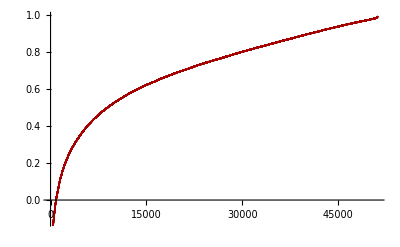

0.699918

```mathematica
test=Table[Correlation[Precip[[day]], ann@Slp[[day]]],{day,Length[Slp]}];
ListPlot[Sort[test]]
Mean[test]
```

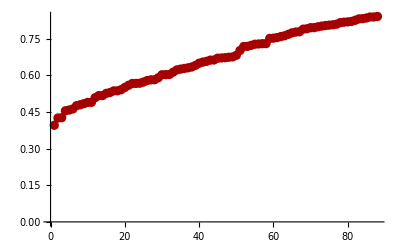

```mathematica
simu=Table[ann@Slp[[day]],{day,Length[Slp]}];
te=Table[Correlation[simu[[;;,i]],Precip[[;;,i]]],{i,88}];
ListPlot[Sort[te]]
```

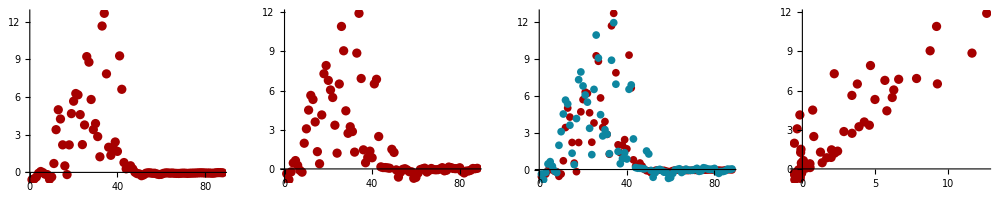
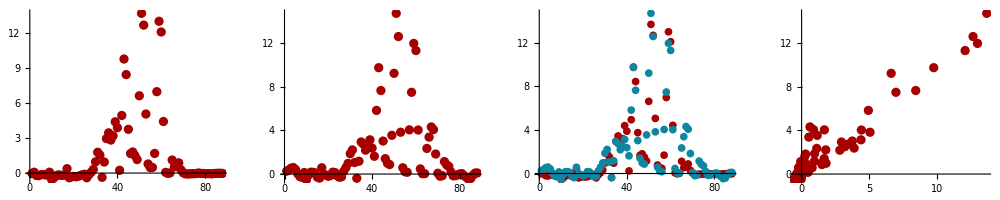
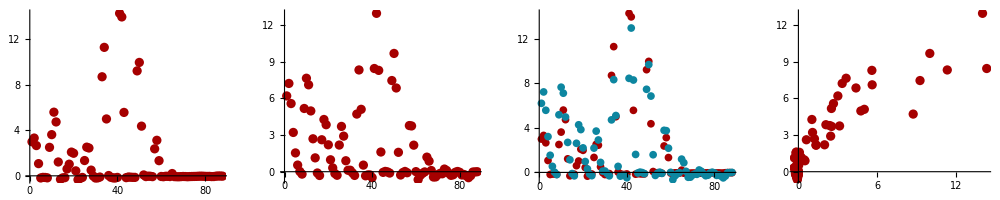
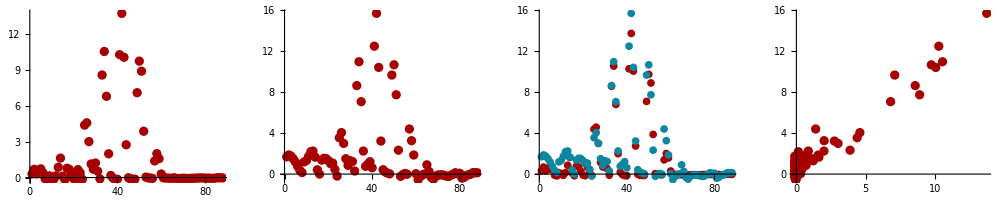
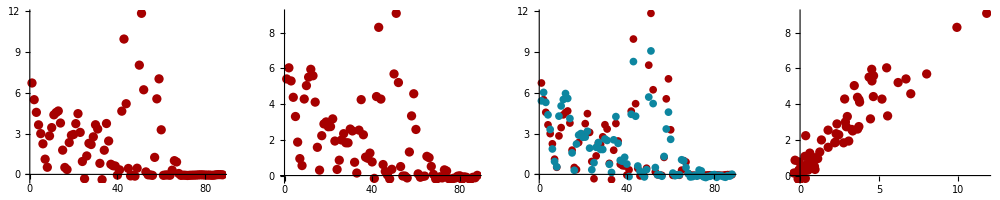
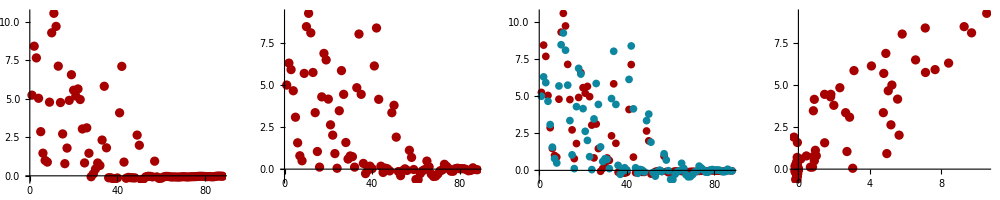
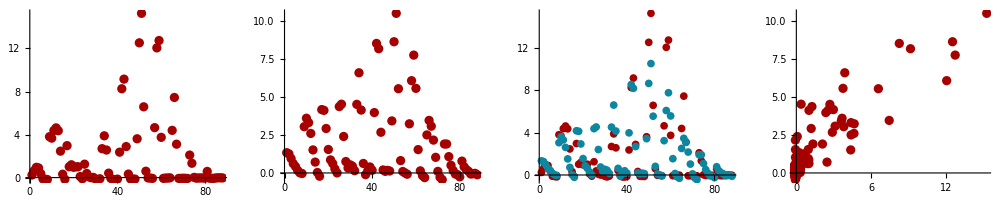
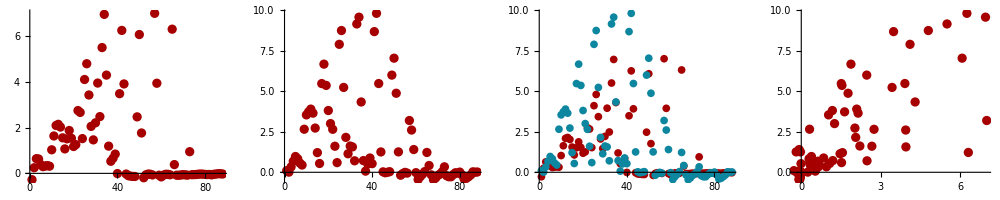

```mathematica
day=Block[{tem=Map[Mean,simu]},
Map[Position[tem,#][[1,1]]&,Sort[tem][[-30;;-1]]]];
Table[
GraphicsRow[{ListPlot[Precip[[day[[i]]]],PlotRange->Full],
			 ListPlot[ann@Slp[[day[[i]]]],PlotRange->Full],
			 ListPlot[{Precip[[day[[i]]]], ann@Slp[[day[[i]]]]},PlotRange->Full],
			 ListPlot[Transpose[{Precip[[day[[i]]]], ann@Slp[[day[[i]]]]}],PlotRange->Full]},
			 ImageSize->1000],{i,Length[day]}]
```

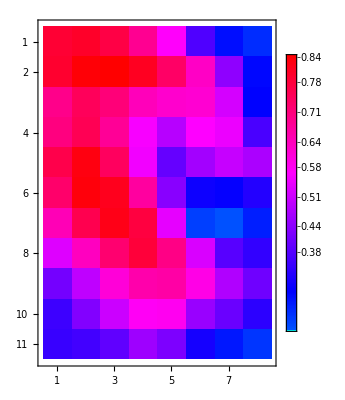

```mathematica
MatrixPlot[ArrayReshape[te,{11,8}],ColorFunction->Hue,
	PlotLegends->Automatic]
```

## Results

## Discussion

## Conclusion

## Operators

```mathematica
PDFPlot[data_]:=Block[{𝒟},
	𝒟 = SmoothKernelDistribution[data];
	Table[Plot[f[𝒟, x], {x, Min[data], Max[data]}, 
	PlotLabel -> f,PlotRange->Full], {f, {PDF, CDF}}]]
```

```mathematica
SetDirectory["/Users/lambda/Documents/S2S/Results"];
Export["ANN.txt",ann]
```

ANN.txt

It's not complicated, it's just a lot of it.

```mathematica
0.00000004*20000
```

0.0008

## Network Structure

```mathematica
Precip=Block[{tempt=Map[Select[Flatten[#],NumberQ]&,Flatten[precip,1]],m,v},
	 v=Sqrt[Variance[tempt]];
	 m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[Precip]
```

{21550,1450}

```mathematica
SLP=Block[{tempt=Flatten[slp,1],m,v},
	v=Sqrt[Variance[tempt]];
	m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[SLP]
```

{21550,16,11}

```mathematica
winter=Flatten[Table[{Range[1+year*365,90+year*365],Range[275+year*365,365+year*365]},{year,0,58}]];
```

```mathematica
Precip=Precip[[winter]];
SLP=SLP[[winter]];
```

```mathematica
CNN=NetInitialize[NetChain[{ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2,1],
						 ConvolutionLayer[1, 3], 
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.5],
						 BatchNormalizationLayer[],
						 900,
						 ElementwiseLayer[Ramp],
						 900,
						 ElementwiseLayer[Ramp],
						 1450,
						 BatchNormalizationLayer[]},  
					"Input" -> {1,16,11}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[SLP]*0.7]
```

7475

```mathematica
ann = NetTrain[CNN,
	Map[{#}&,SLP[[1;;ptraining]]] -> Precip[[1;;ptraining]],
	ValidationSet->Table[{SLP[[i]]}->Precip[[i]],{i,ptraining,Length[SLP]}],
	Method->"ADAM",
	BatchSize->200,
	MaxTrainingRounds -> 2000]
```

NetChain[]

```mathematica
Dimensions[SLP]
```

{10679,16,11}

```mathematica
simu=Table[ann@{SLP[[day]]},{day,Length[SLP]}];
```

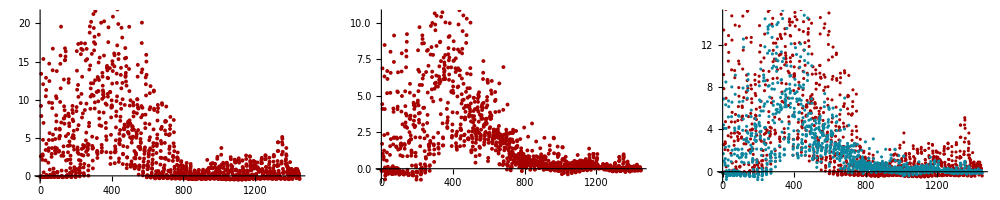

```mathematica
day=3419;
GraphicsRow[{ListPlot[Precip[[day]]],ListPlot[ann@{SLP[[day]]}],ListPlot[{Precip[[day]],ann@{SLP[[day]]}}]},
	ImageSize->1000]
```

```mathematica
test=Table[Correlation[ann@{SLP[[day]]},Precip[[day]]],{day,Length[SLP]}];
```

```mathematica
MinMax[test]
```

{-0.656667,0.973372}

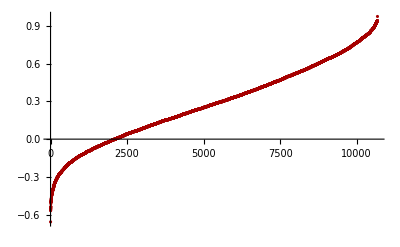

```mathematica
ListPlot[Sort[test]]
```

```mathematica
Position[test,Max[test[[1;;365*10]]]]
```

{{3419}}

The initial layers in CNN are used for seeking and optimizing inputs’ spatial features, which are fed to the rest layers for classification/regression tasks.  

Its flexible architecture allows structures and layer types. ATTRACTS THE ATTENTION OF THE GEOCOMMUNITy
different types of layers have evolved for
various purposes. One type of layer that warrants particular mention is convolutional
layers [48]. 

Among various deep learning architectures, Convolutional Neural Network(CNN) is especially suited for processing spatial structured data. The initial layers in CNN are used for seeking and optimizing inputs’ features, which are fed to the rest layers for classification/regression tasks.  








This is due to the frequent pass of extratropical cyclones within relatively confined regions.

This is due to the frequent pass of extratropical cyclones within relatively confined regions. However, the strong correlation becomes invalid at finer spatial temporal scales\cite[], making it difficult to attribute precipitation to the coverage, location, intensity and spatial structure of characteristic circulation patterns.  Such relationship is important since it acts as verification for parameterization schemes and probe for model diagnosis and improvements. 


Despite their effectiveness, these classical methods are very often limited when faced with high dimensional nonlinear correlated data. Temporal scale!! stress it!

Even with classical methods mentioned above, 

Classical synoptical analysis methods, such as correlation analysis and Principal Component Analysis(PCA), have long-been applied for causality detection. 
 1.


insufficient when faced with such spatially distributed high dimensional data. For instance, through a simple correlation field analysis, monthly mean regional average precipitation across United States is directly related to critical area’s Sea Level Pressure(SLP) \cite[1,2,3]. This is due to the frequent pass of extratropical cyclones within relatively confined regions. However, the strong correlation becomes invalid at finer spatial temporal scales\cite[], making it difficult to attribute precipitation to the coverage, location, intensity and spatial structure of characteristic circulation patterns.  Such relationship is important since it acts as verification for parameterization schemes and probe for model diagnosis and improvements. 

diagnosing and improving existed models, understanding 

To quantify their specific contributions can help diagnosing and improving existed models and 

Given the continuity constraints and computing costs, no easy what-if experiments could be conducted to separate the impacts 

To the authors’ knowledge, there is no approach that quantitatively discern the attribution of each aspect regarding QPF.

quantitative causality analysis approach

precipitation change in accordance with the departure of depression center or any other aspect mentioned above
, such as the location, coverage, intensity and spatial structures. 

Diagnose of precipitation estimation error 

Also to attribute precipitation simulation errors, ..






For unresolved sub-grid scale, it is described as a byproduct of moist convection through convective parameterization\cite[]. For grid scale, it is explicitly represented through microphysical parameterization\cite[]. Recent advances in supercomputer are boosting finer resolution that enables resolving cloud without convective parameterization\cite[].


applied for rainfall warning since the dawn of civilization,  

prediction in dynamical weather and climate models depends on 1) the predictability of pressure or geopotential height for the forecasting period\cite[] and 2) the successive work of interpreting the pressure field in terms of precipitation events\cite[].  This strategy dates back to the early 20th century when barometric observations were interpolated in space and extrapolated along time, based on which semi-quantitative weather predictions were drawn\cite[]. Since then, the first task has been transforming from empirical inferences to accurate science due to the elucidation of physical laws, increasing computing power and densifying observation networks\cite[]. Such change poses both opportunities and challenges on the subsidiary work of connecting precipitation events to circulation. 	
Precipitation processes are parameterized to close the governing equations for iterative discretized simulation. For unresolved sub-grid scale, it is described as a byproduct of moist convection through convective parameterization\cite[]. For grid scale, it is explicitly represented through microphysical parameterization\cite[]. Recent advances in supercomputer are boosting finer resolution that enables resolving cloud without convective parameterization\cite[].
Given its increasing complexity, detailed computing inevitably blurs the hidden cause-and-effect relationship in precipitation generation. The “big data” provided by numerical simulation, reanalysis and observation networks requires better causation analysis for people to digest and realize their use. Classic synoptical analysis methods are very-often insufficient when faced with such spatially distributed high dimensional data. For instance, through a simple correlation field analysis, monthly mean regional average precipitation across United States is directly related to critical area’s Sea Level Pressure(SLP) \cite[1,2,3]. This is due to the frequent pass of extratropical cyclones within relatively confined regions. However, the strong correlation becomes invalid at finer spatial temporal scales\cite[], making it difficult to attribute precipitation to the coverage, location, intensity and spatial structure of characteristic circulation patterns.  Such relationship is important since it acts as verification for parameterization schemes and probe for model diagnosis and improvements. 
The past decades have seen a revolution in statistical analysis as it keeps absorbing machine learning techniques to meet the big data challenge. Most machine learning paradigms have found their applications in geoscience, the community in turn learns to treat geo variables and their connections as information and information flows\cite[myself]. Deep learning is branch of machine learning that attracts the most attention for its outstanding fitting capacity. Mathematically it is a hierarchical superposition of basic non-linear units(named Neurons for their biological inspiration) that map input tensors to output tensors. The multi-layer feedforward structure allows attributing the mapping error to each computing unit by applying calculus Chain Rule. Parameters(connecting weights and biases) can thus be adjusted accordingly. Among various deep learning architectures, Convolutional Neural Network(CNN) is especially suited for processing spatial structured data. The initial layers in CNN are used for seeking and optimizing inputs’ features, which are fed to the rest layers for classification/regression tasks.  

Geological field data usually hold spatial structures. While these structures are often ignored in lumped ANN, they could be utilized for more compact and effective information abstraction in CNN. Existed geological applications of CNN include short range weather prediction[24], precipitation nowcasting[25] and extreme weather detection[26, 27]. We illustrate how CNN can be applied for precipitation projection using pressure field here.


becomes more and more overlapped with machine learning to meet the big data challenge.  

The difference between the two has reduced significantly over the past decade. 
impacted by machine learning techniques. 


which is due to the frequent pass of storm tracks. However, 


Specific to the problem of precipitation-circulation connection, synoptical analysis has shown that at monthly scale, 

The past decade has seen explosive advance is machine learning, especially deep learning. Why? list the several reasons. See with the help of algorithms. It equipped human with deep insight when observing. 


A balance between grid-scale computing and macro-scale causation analysis is required. 
Classical statistical synoptical analysis methods include 

, which requires supplement from statistical synoptical analysis.


A gap is expanding 

A balance between detailed parameterization and macro-scale causation analysis is required.  meet the challenges

Despite their scientific illumination and pragmatic importance,  the detailed computing inevitably blurs the cause-and-effect relationship hidden in meteorological phenomena. Statistical synoptic analysis has long been an important supplement for interpreting cause-and-effect relationship hidden in meteorological phenomena\cite[],providing diagnosis and improvement directions. 

The past decade has seen explosive advance is machine learning, especially deep learning. Why? list the several reasons. See with the help of algorithms. It equipped human with deep insight when observing. 






The atmospheric process character greatly depends upon geographical
latitude defining radiation conditions, type and state of the underlying
surface, the region orographic features, etc.

Every of these approaches has both advantages
and disadvantages and, correspondingly, its field of application

Despite the detailling trend., the detail blur the cause-and -effect relationship in synoptic analysis. (we can not hack into numerical models unless doing “whatif” experiments, which involves too much variabilities and computing burdens)
  For instance, distance, intensity, orographic
Statistical methods in understanding , diagnosis correlation field. and PCA. 
a gap fro integrating synoptic and dynamic meteorology\cite[].
Synoptic: 

Dynamical precipitation modelling is usually achieved through the cooperation of convective and microphysical parameterization schemes



illustrating cause-and-effect relationship

Parameterization. Specific to precipitation
storm track

The past decade has seen explosive advance is machine learning, especially deep learning. Why? list the several reasons. See with the help of algorithms. It equipped human with deep insight when observing. 

pre-fixed features to trainable features. 

we use CNN to illustrate the following questions:

1)
2)
3)

dawn of modern meteorology 


early 20th century (Bjerknes)  and have ?? Empirical Extrapolating geopotential height field along time to numerical prediction. It helped the second task. (Existed works  connect to this target) tell about history of extrapolating during the very initial weather forecast semi-quantitative.

subsidiary work of interpreting the pressure field in terms of weather also demands  a large share of attention and is somewhat complex.

Correlation field.

the second task: 
1) focusing on prediction
  	1.1) parameterization
		microphysics
		cumulative parameter 
  	1.2) cloud resolving models
2) focusing on interpretation
	2.1) Correlation Field
	2.2) PCA Combined PCA
What have been done in interpreting? semi-quantitative
what are their drawbacks?
This study is directed toward one aspect of the subsidiary problem. 
Deep learning quantitative observation.	
1) understanding
2) diagnosis: Typical pressure structure, intensity, distance, evolution 
3) improvement 
what are the key difficulties?
 p.d.f. of precipitation
 
 

 	1. is it raining?
 	2. if rains, how heavy?

Basic Deep Learning algorithms such as fully connected Artificial Neural Network(ANN) have long been used in geo community for classification/regression problems[38, 39, 40]. Mathematically they are hierarchical superposition of basic non-linear units(named Neurons for their biological inspiration) that map input vectors to output vectors. The multi-layer feedforward structure allows attributing the mapping error to each computing unit by applying calculus Chain Rule. The parameters(connection weights and biases) can thus be ad- justed accordingly.
Geological field data usually hold spatial structures. While these structures are often ignored in lumped ANN, they could be utilized for more compact and effective information abstraction in CNN. This is achieved through sequentially applying two peculiar matrix operators, namely convolutional layer and pooling layer.
Each convolutional layer operator filters the input field with a same kernel, which is a m×n matrix consisted
of weight parameters. m and n are called kernel size.
The pooling layer acts as a sub-sampling layer, which can also be viewed as
 a convolutional layer with a maximum value sel	ection kernel.
While most pattern recognition algorithms seek prefixed/engineered fea- tures(or in other words, prefixed/engineered kernels), the kernels in CNN could be optimized through backpropagation[20], just as the weights in fully con- nected ANN. Thus both the feature selection and later classification/regression process are trainable. Through optimized convolution and pooling operations, CNN maintains and extracts input’s structures toward better representation for a given target. Besides, the sharing parameter scheme can effectively reduce overfitting by lowering model complexity. We also included state-of-the-art reg- ularization methods, such as dropout[42] and batch normalization[43], to further balance training and test performances.
Specific to the research question here, the SLP field data was fed to a CNN. Through sequentially convolution and pooling operations, we reached a new representation of the original field data, where important pressure structure in- formation at different locations is strengthened. It was flattened and further processed through a fully connected ANN to regress precipitation, where the location information is stressed by attributing different weights to neurons from different positions. Figure 6 illustrated how CNN worked on SLP using meteo- rological records of December,2015 as an example.
The specific CNN architecture and hyperparameters were listed in Table 2. Hyperparameters were chose through trial and error.
The
Their Euclidean Distance was used as objective function for parameter opti- mization. The Stocahstic Gradient Descent(SGD) method[44] was applied for parameter optimization.
To train the network, 68 years’ cool season(October to March from 1948 to 2015) monthly NCEP reanalysis SLP field data and CPC precipitation data were divided into two parts. The first 48 years were taken as training set leaving rest to be the test set. Cool season months were not separated in training but results were evaluated month by month.
The CNN construction and optimization were implemented using deep learn- ing toolkits developed by Wolfram Mathematica[45].

```mathematica
Export["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/download.sh",TableForm[Table["wget ftp://ftp.cdc.noaa.gov/Datasets/ncep.reanalysis/pressure/hgt."<>ToString[year]<>".nc",
	{year,1948,2017}]],"List"]
```

/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/download.sh

```mathematica
Export["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/extract.sh",
	TableForm[Table["scp baoxianp@hpc.oit.uci.edu:/pub/baoxianp/GPH/hgt."<>ToString[year]<>".nc .",
	{year,1948,2017}]],"List"]
```

/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/extract.sh